# Упражнение 7. Интерполиране с обобщени полиноми

### Да се намери подходяща функция, която интерполира данните за развитие на бактериална популация:

t,h | 1 | 2 | 3 | 4 | 5
клетки (x1000) | 1 | 12 | 110 | 1037 | 12218

```mathematica
ϕ[x_]:=a0+a1*E^x+a2*E^(2x)+a3*E^(3x)+a4*E^(4x)
sol=NSolve[{{ϕ[1]==1,ϕ[2]==12,ϕ[3]==110,ϕ[4]==1037,ϕ[5]==12218}},{a0,a1,a2,a3,a4}]
```

{{a0→0.10506,a1→-0.382376,a2→0.25728,a3→0.00165052,a4→2.4983×10^-6}}

0.10506-0.382376 ⅇ^x+0.25728 ⅇ^(2 x)+0.00165052 ⅇ^(3 x)+2.4983×10^-6 ⅇ^(4 x)

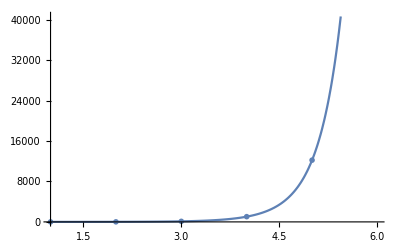

```mathematica
ϕ[x_]=ϕ[x]/.sol[[1]]
plot1=Plot[ϕ[x],{x,1,6}];
plot2=ListPlot[{{1,1},{2,12},{3,110},{4,1037},{5,12218}},PlotMarkers->●];
Show[plot1,plot2]
```